```mathematica
β[ω_,δ_,t_,ϵ_]:={{ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0,0,0,0},{-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0,0,0},{0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0,0},{0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0,0},{0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0,0},{0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0,0},{0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0,0},{0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0,0},{0,0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t,0},{0,0,0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω,-t},{0,0,0,0,0,0,0,0,0,-t,ⅈ δ-ϵ+ω}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0,0,0,0,0},{0,t,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,t,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,t,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,t,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,t,0},{0,0,0,0,0,0,0,0,0,0,0}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,t,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,t,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,t,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,t,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,t}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:=T1[t],T2:=T2[t]},Do[J=Inverse[IdentityMatrix[11]-A.T1.Inverse[IdentityMatrix[11]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

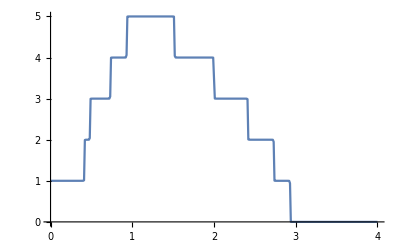
{1.27253,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
σ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ3[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ4[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ6[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ7[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ8[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ11[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ12[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ13[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
σσ14[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[t].SL[ω,δ,t,ϵ].T1[t]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[t].Sl11.T2[t]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[t].Sl12.T1[t]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[t].Sl13.T2[t]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[t].Sl14.T1[t]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[t].Sl15.T2[t]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[t].Sl16.T1[t]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[t].Sl17.T2[t]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[t].SR[ω,δ,t,ϵ].T1[t]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].Sl18.T1[t]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[t].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
If[Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]>5,5,Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]]
```

```mathematica
Clear[kk314,kk313,kk312,kk311,kk310,kk39,kk38,kk37,kk36,kk35,kk34,kk33,kk32,kk31]
```

```mathematica
k314[ω_,ϵ1_]:=k314[ω,ϵ1]=Append[{},Table[σ14[ω,0.001,1,0,ϵ1],{i,50}]];
k313[ω_,ϵ1_]:=k313[ω,ϵ1]=Append[{},Table[σ13[ω,0.001,1,0,ϵ1],{i,50}]];
k312[ω_,ϵ1_]:=k312[ω,ϵ1]=Append[{},Table[σ12[ω,0.001,1,0,ϵ1],{i,50}]];
k311[ω_,ϵ1_]:=k311[ω,ϵ1]=Append[{},Table[σ11[ω,0.001,1,0,ϵ1],{i,50}]];
k310[ω_,ϵ1_]:=k310[ω,ϵ1]=Append[{},Table[σ10[ω,0.001,1,0,ϵ1],{i,50}]];
k39[ω_,ϵ1_]:=k39[ω,ϵ1]=Append[{},Table[σ9[ω,0.001,1,0,ϵ1],{i,50}]];
k38[ω_,ϵ1_]:=k38[ω,ϵ1]=Append[{},Table[σ8[ω,0.001,1,0,ϵ1],{i,50}]];
k37[ω_,ϵ1_]:=k37[ω,ϵ1]=Append[{},Table[σ7[ω,0.001,1,0,ϵ1],{i,50}]];
k36[ω_,ϵ1_]:=k36[ω,ϵ1]=Append[{},Table[σ6[ω,0.001,1,0,ϵ1],{i,50}]];
k35[ω_,ϵ1_]:=k35[ω,ϵ1]=Append[{},Table[σ5[ω,0.001,1,0,ϵ1],{i,50}]];
k34[ω_,ϵ1_]:=k34[ω,ϵ1]=Append[{},Table[σ4[ω,0.001,1,0,ϵ1],{i,50}]];
k33[ω_,ϵ1_]:=k33[ω,ϵ1]=Append[{},Table[σ3[ω,0.001,1,0,ϵ1],{i,50}]];
k32[ω_,ϵ1_]:=k32[ω,ϵ1]=Append[{},Table[σ2[ω,0.001,1,0,ϵ1],{i,50}]];
k31[ω_,ϵ1_]:=k31[ω,ϵ1]=Append[{},Table[σ1[ω,0.001,1,0,ϵ1],{i,50}]];kk314[ω_,ϵ1_]:=kk314[ω,ϵ1]=Append[{},Table[σσ14[ω,0.001,1,0,ϵ1],{i,50}]];
kk313[ω_,ϵ1_]:=kk313[ω,ϵ1]=Append[{},Table[σσ13[ω,0.001,1,0,ϵ1],{i,50}]];
kk312[ω_,ϵ1_]:=kk312[ω,ϵ1]=Append[{},Table[σσ12[ω,0.001,1,0,ϵ1],{i,50}]];
kk311[ω_,ϵ1_]:=kk311[ω,ϵ1]=Append[{},Table[σσ11[ω,0.001,1,0,ϵ1],{i,50}]];
kk310[ω_,ϵ1_]:=kk310[ω,ϵ1]=Append[{},Table[σσ10[ω,0.001,1,0,ϵ1],{i,50}]];
kk39[ω_,ϵ1_]:=kk39[ω,ϵ1]=Append[{},Table[σσ9[ω,0.001,1,0,ϵ1],{i,50}]];
kk38[ω_,ϵ1_]:=kk38[ω,ϵ1]=Append[{},Table[σσ8[ω,0.001,1,0,ϵ1],{i,50}]];
kk37[ω_,ϵ1_]:=kk37[ω,ϵ1]=Append[{},Table[σσ7[ω,0.001,1,0,ϵ1],{i,50}]];
kk36[ω_,ϵ1_]:=kk36[ω,ϵ1]=Append[{},Table[σσ6[ω,0.001,1,0,ϵ1],{i,50}]];
kk35[ω_,ϵ1_]:=kk35[ω,ϵ1]=Append[{},Table[σσ5[ω,0.001,1,0,ϵ1],{i,50}]];
kk34[ω_,ϵ1_]:=kk34[ω,ϵ1]=Append[{},Table[σσ4[ω,0.001,1,0,ϵ1],{i,50}]];
kk33[ω_,ϵ1_]:=kk33[ω,ϵ1]=Append[{},Table[σσ3[ω,0.001,1,0,ϵ1],{i,50}]];
kk32[ω_,ϵ1_]:=kk32[ω,ϵ1]=Append[{},Table[σσ2[ω,0.001,1,0,ϵ1],{i,50}]];
kk31[ω_,ϵ1_]:=kk31[ω,ϵ1]=Append[{},Table[σσ1[ω,0.001,1,0,ϵ1],{i,50}]]
```

```mathematica
ρ3[ω_,ϵ1_]:=Join[Mean[k31[ω,ϵ1]],Mean[k32[ω,ϵ1]],Mean[k33[ω,ϵ1]],Mean[k34[ω,ϵ1]],Mean[k35[ω,ϵ1]],Mean[k36[ω,ϵ1]],Mean[k37[ω,ϵ1]],Mean[k38[ω,ϵ1]],Mean[k39[ω,ϵ1]],Mean[k310[ω,ϵ1]],Mean[k311[ω,ϵ1]],Mean[k313[ω,ϵ1]],Mean[k314[ω,ϵ1]],Mean[kk31[ω,ϵ1]],Mean[kk32[ω,ϵ1]],Mean[kk33[ω,ϵ1]],Mean[kk34[ω,ϵ1]],Mean[kk35[ω,ϵ1]],Mean[kk36[ω,ϵ1]],Mean[kk37[ω,ϵ1]],Mean[kk38[ω,ϵ1]],Mean[kk39[ω,ϵ1]],Mean[kk310[ω,ϵ1]],Mean[kk311[ω,ϵ1]],Mean[kk313[ω,ϵ1]],Mean[kk314[ω,ϵ1]]]
```

```mathematica
Timing[Mean[ρ3[1.25,0.5]]]
```

{18.8969,4.57887}

```mathematica
Export["3imp3.csv",Table[{ω,Mean[ρ3[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

3imp3.csv

```mathematica
Export["3imp4.csv",Table[{ω,Mean[ρ3[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

3imp4.csv

```mathematica
Export["3imp5.csv",Table[{ω,Mean[ρ3[ω,0.5]]},{ω,Range[0,4,0.01]}]]
```

3imp5.csv

```mathematica
Export["3imp6.csv",Table[{ω,Mean[ρ3[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

3imp6.csv

```mathematica
Export["3imp7.csv",Table[{ω,Mean[ρ3[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

3imp7.csv

```mathematica
Export["3imp8.csv",Table[{ω,Mean[ρ3[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

3imp8.csv

```mathematica
Export["3imp9.csv",Table[{ω,Mean[ρ3[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

3imp9.csv

```mathematica
Timing[Export["3imp1.csv",Table[{ω,Mean[ρ3[ω,1]]},{ω,Range[0,4,0.01]}]]]
```

{8219.61,3imp1.csv}